```mathematica
AppendTo[$Path,"/Users/scott/projects/toolkit/algebra-spiders/src/main/mathematica/"];
```

```mathematica
<<Spiders`
```

Loading Spiders` version 2015-06-18 ...

```mathematica
ImageCrop[ImageCrop[ImageRotate[Import["~/projects/exceptional/notes/bases.pdf"]⟦1⟧],{Full,500}],{Full,275},Top]
```

-Graphics-

```mathematica
S=PlanarGraphs@spider[]
```

«JavaObject[net.tqft.toolkit.algebra.spiders.DiagramSpider$$anon$1]»

```mathematica
#@toString[]&/@ReducedDiagrams[BraidedTrivalent⟦1⟧,2,0,0]
```

{PlanarGraph(2,Vector(List((1,2), (1,3))),List(),0)}

```mathematica
#@toString[]&/@ReducedDiagrams[BraidedTrivalent⟦1⟧,3,0,1]
```

{PlanarGraph(5,Vector(List((2,5), (4,6), (3,7)), List((2,6), (3,5), (4,7))),List((1,0)),0)}

```mathematica
#@toString[]&/@ReducedDiagrams[BraidedTrivalent⟦1⟧,4,0,0]~Join~ReducedDiagrams[BraidedTrivalent⟦1⟧,4,0,2]~Join~ReducedDiagrams[BraidedTrivalent⟦1⟧,4,1,0]⟦{1}⟧
```

{PlanarGraph(3,Vector(List((1,3), (1,5), (2,3), (2,4))),List(),0),PlanarGraph(3,Vector(List((1,3), (2,5), (2,4), (1,5))),List(),0),PlanarGraph(8,Vector(List((3,8), (5,11), (6,9), (4,10)), List((4,8), (6,10), (7,9)), List((3,11), (7,8), (5,9))),List((1,0), (1,0)),0),PlanarGraph(8,Vector(List((6,8), (4,9), (3,11), (5,10)), List((3,10), (4,11), (7,9)), List((5,8), (7,10), (6,9))),List((1,0), (1,0)),0),PlanarGraph(6,Vector(List((2,6), (5,8), (4,9), (3,7)), List((5,9), (2,8), (3,6), (4,7))),List((2,0)),0)}

```mathematica
DrawPlanarGraph/@ReducedDiagrams[BraidedTrivalent⟦1⟧,5,0,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@ReducedDiagrams[BraidedTrivalent⟦1⟧,5,0,3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@ReducedDiagrams[BraidedTrivalent⟦1⟧,5,1,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@ReducedDiagrams[BraidedTrivalent⟦1⟧,5,1,3]
```

```mathematica
#@toString[]&/@ReducedDiagrams[BraidedTrivalent⟦1⟧,5,0,1]~Join~ReducedDiagrams[BraidedTrivalent⟦1⟧,5,0,3]~Join~ReducedDiagrams[BraidedTrivalent⟦1⟧,5,1,1]⟦{1,2,3,4,-2}⟧~Join~ReducedDiagrams[BraidedTrivalent⟦1⟧,5,1,3]⟦{7}⟧
```

{PlanarGraph(6,Vector(List((2,6), (4,9), (3,8), (5,6), (5,7)), List((2,9), (3,6), (4,8))),List((1,0)),0),PlanarGraph(6,Vector(List((5,6), (5,7), (2,6), (4,9), (3,8)), List((2,9), (3,6), (4,8))),List((1,0)),0),PlanarGraph(6,Vector(List((3,6), (2,9), (5,7), (5,8), (4,7)), List((2,7), (3,9), (4,6))),List((1,0)),0),PlanarGraph(6,Vector(List((5,6), (2,7), (4,8), (3,9), (5,7)), List((2,8), (3,7), (4,9))),List((1,0)),0),PlanarGraph(6,Vector(List((4,6), (5,7), (5,8), (3,7), (2,9)), List((2,6), (3,9), (4,7))),List((1,0)),0),PlanarGraph(11,Vector(List((5,11), (7,15), (4,13), (8,12), (6,14)), List((4,12), (10,13), (9,11)), List((6,11), (8,14), (9,12)), List((5,15), (10,11), (7,13))),List((1,0), (1,0), (1,0)),0),PlanarGraph(11,Vector(List((7,11), (4,13), (8,12), (6,14), (5,15)), List((4,12), (10,13), (9,15)), List((6,15), (8,14), (9,12)), List((5,11), (10,15), (7,13))),List((1,0), (1,0), (1,0)),0),PlanarGraph(11,Vector(List((7,11), (5,14), (6,15), (8,13), (4,12)), List((4,11), (10,12), (9,15)), List((5,15), (7,14), (9,11)), List((6,13), (10,15), (8,12))),List((1,0), (1,0), (1,0)),0),PlanarGraph(11,Vector(List((4,11), (8,12), (6,13), (5,15), (7,14)), List((4,12), (10,11), (9,15)), List((6,15), (8,13), (9,12)), List((5,14), (10,15), (7,11))),List((1,0), (1,0), (1,0)),0),PlanarGraph(11,Vector(List((6,11), (5,15), (7,14), (4,13), (8,12)), List((4,12), (10,13), (9,15)), List((6,15), (8,11), (9,12)), List((5,14), (10,15), (7,13))),List((1,0), (1,0), (1,0)),0),PlanarGraph(9,Vector(List((3,9), (5,12), (6,10), (7,13), (4,11)), List((4,9), (7,11), (6,13), (8,10)), List((3,12), (8,9), (5,10))),List((2,0), (1,0)),0),PlanarGraph(9,Vector(List((3,9), (6,11), (5,13), (7,12), (4,10)), List((3,11), (4,9), (8,10)), List((7,10), (5,12), (6,13), (8,11))),List((1,0), (2,0)),0),PlanarGraph(9,Vector(List((3,9), (6,13), (5,11), (7,12), (4,10)), List((6,11), (3,13), (4,9), (8,10)), List((5,12), (8,11), (7,10))),List((2,0), (1,0)),0),PlanarGraph(9,Vector(List((4,9), (7,10), (5,13), (6,11), (3,12)), List((4,10), (3,9), (6,12), (8,11)), List((5,11), (7,13), (8,10))),List((2,0), (1,0)),0),PlanarGraph(9,Vector(List((3,9), (6,12), (5,13), (7,10), (4,11)), List((4,9), (7,11), (8,10)), List((3,12), (8,9), (5,10), (6,13))),List((1,0), (2,0)),0),PlanarGraph(14,Vector(List((7,14), (8,17), (9,16), (6,18), (5,19)), List((8,16), (12,17), (13,15)), List((9,18), (13,16), (11,15)), List((7,17), (10,14), (12,15)), List((10,15), (5,14), (6,19), (11,18))),List((1,0), (1,0), (1,0), (2,0)),0)}

```mathematica
DrawPlanarGraph/@(basis0=ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,0])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis1=Table[S@rotate[S@tensor[PlanarGraphs@crossing[],PlanarGraphs@strand[]],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis2=Table[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@inverseCrossing[],1],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis3={PlanarGraphs@Reidemeister3[]@head[]})
```

{-Graphics-}

```mathematica
DrawPlanarGraph/@(basis4=ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,2])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis5=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@trivalentVertex[],1],2],PlanarGraphs@trivalentVertex[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis6={S@multiply[PlanarGraphs@inverseCrossing[],S@rotate[S@multiply[PlanarGraphs@crossing[],S@rotate[S@tensor[PlanarGraphs@trivalentVertex[],PlanarGraphs@trivalentVertex[]],1],2],3],2]})
```

{-Graphics-}

```mathematica
DrawPlanarGraph/@(basis7=Table[S@rotate[S@multiply[PlanarGraphs@I[],PlanarGraphs@crossing[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis8=Table[S@rotate[S@multiply[PlanarGraphs@H[],PlanarGraphs@crossing[],1],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis9=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@inverseCrossing[],1],2],PlanarGraphs@H[],2],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis10=Table[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@inverseCrossing[],PlanarGraphs@trivalentVertex[],1],3],PlanarGraphs@trivalentVertex[],1],k],{k,0,2}])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis11=Cases[ReducedDiagrams[BraidedTrivalent⟦1⟧,6,0,4],g_/;!(g@Subgraphs[]@apply[polygon[4]]@excisions[]@hasNext[])])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis12=Table[S@rotate[S@multiply[S@rotate[S@multiply[S@rotate[S@multiply[PlanarGraphs@crossing[],PlanarGraphs@trivalentVertex[],1],2],PlanarGraphs@trivalentVertex[],1],5],PlanarGraphs@I[],2],k],{k,0,5}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis13=Table[S@rotate[S@multiply[PlanarGraphs@fromString["PlanarGraph(14,Vector(List((8,14), (9,15), (7,16), (6,18), (5,19), (10,17)), List((5,17), (11,19), (13,15)), List((6,19), (12,18), (11,15)), List((8,15), (10,14), (13,17)), List((7,18), (9,16), (12,15))),List((1,0), (1,0), (1,0), (1,0)),0)"],PlanarGraphs@crossing[],2],k],{k,0,3}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawPlanarGraph/@(basis14={polygon[6]})
```

{-Graphics-}

```mathematica
basis=basis0~Join~basis1~Join~basis2~Join~basis3~Join~basis4~Join~basis5~Join~basis6~Join~basis7~Join~basis8~Join~basis9~Join~basis10~Join~basis11~Join~basis12~Join~basis13~Join~basis14;
```

```mathematica
Length[basis]
```

80

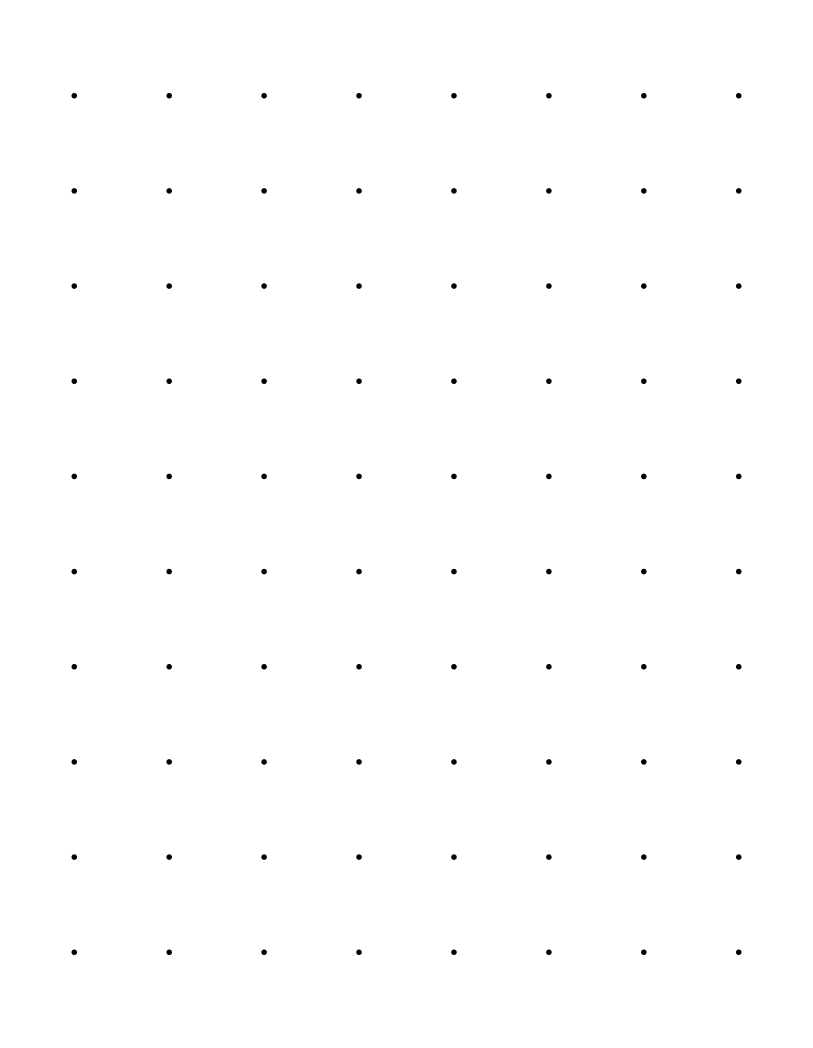

```mathematica
GraphicsGrid[Partition[DrawPlanarGraph/@basis,8]]
```

```mathematica
closed=Union[Flatten[Outer[S@multiply[#1,#2,6]&,basis,basis]]]
```

{«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,6391,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»,«JavaObject[net.tqft.toolkit.algebra.spiders.PlanarGraph]»}
 |  |  |  |

```mathematica
Length/@Table[Symbol["basis"<>ToString[k]],{k,0,14}]
```

{5,6,3,1,15,6,1,6,6,3,3,14,6,4,1}

```mathematica
Total[%]
```

80